VectorPlot::nonopt: Options expected (instead of VectorScale {0.03,0.03,None}) beyond position 3 in VectorPlot[{1,F[x,y]},{x,-4,4},{y,-4,4},VectorStyle→{Thick,Red},VectorScale {0.03,0.03,None},VectorPoints→25]. An option must be a rule or a list of rules.

Show::gtype: VectorPlot is not a type of graphics.

Show[VectorPlot[{1,F[x,y]},{x,-4,4},{y,-4,4},VectorStyle→{Thick,Red},VectorScale {0.03,0.03,None},VectorPoints→25]]

VectorColorFunction::cfun: Value of option ColorFunction -> None VectorScale→{0.03,0.03,None} is not a valid color function, or a gradient ColorData entity.

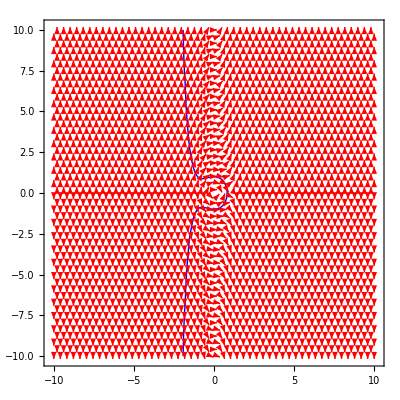

```mathematica
f[x_,y_]:=((x^2+y^2)*x^2-x)/y;
g[x_,y_]:=((x^2+y^2)*e^((2x^3)/3));
Show[VectorPlot[{1,f[x,y]},{x,-10,10},{y,-10,10},VectorStyle ->Red, VectorColorFunction -> None VectorScale-> {.03,.03,None},VectorPoints-> 50], ContourPlot[(x^2+y^2)*Exp[x^3*2/3]==1,{x,-10,10},{y,-10,10},  ContourShading -> None, ContourStyle->{Thick, Blue}]]
```

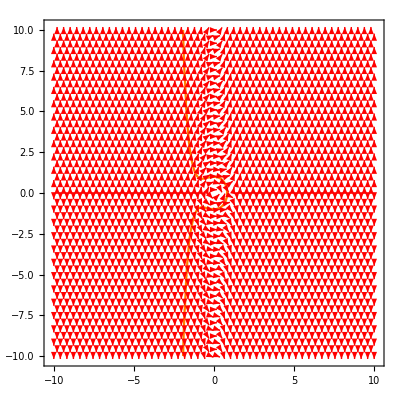
```mathematica
-Graphics-
Show[%111,Background->RGBColor[0.,0.09,0.44]]
```

-Graphics-

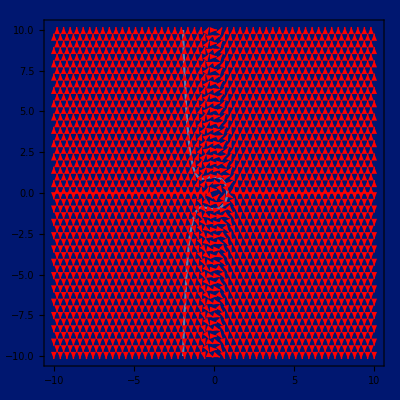

```mathematica
Show[%118,Axes->True,AxesStyle->White]
```

```mathematica
Show[%111,Background->RGBColor[0.,0.09,0.44]]
```

-Graphics-